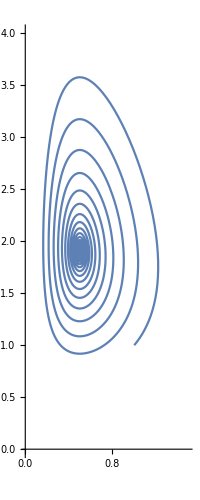

```mathematica
(* Parâmetros iniciais *)
a = 2;
b = 3;
c = 1;
d = 2;
K = 10;
xt = 5;
yt = 5;
theta1 = 0.3;
theta2 = 0.2;
tau = 0.3;

(* Define as funções  epsilon1 e epsilon2 *)
epsilon1[x_, y_] := Piecewise[{{0, x < xt}, {theta1, x > xt && y < yt}, {theta2, x > xt && y > yt}}]
epsilon2[x_, y_] := Piecewise[{{0, x < xt}, {tau, x > xt && y < yt}, {0, x > xt && y > yt}}]

(* Define sistema de equação presa-predador *)
system = {x'[t] == a*x[t]*(1 - x[t]/K) - b*x[t]*y[t] - epsilon1[x[t], y[t]]*x[t], y'[t] == d*x[t]*y[t] - c*y[t] + epsilon2[x[t], y[t]]};

(* Define condições iniciais *)
initcond = {x[0] == 5, y[0] == 10};

(* Resolve as equações *)
solution = NDSolve[Join[system, initcond], {x, y}, {t, 0, 100}];

ParametricPlot[Evaluate[{x[t], y[t]} /. solution], {t, 0, 100}, PlotRange -> {{0, 1.5}, {0, 4}}]
```